```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* 
	This Notebook is dedicated to plot the geodesics of a test particle, massive or massless, in the swirling universe space.
	There are some comments on the organization of the notebook, that may be helpful to the reader. In any case of doubts, please don't hesitate to contact the autors.  
*)
```

```mathematica
(* Defining the orbit parameters *)
ClearAll[t,ρ,z,ϕ]
ClearAll[χ,j,ee,ll,k,orbitparams]
orbitparams=N[{χ->-1,j->√(1/20),ee->3,ll->1,k->22/10},40];
(* Initial Conditions and orbit signs *)
ClearAll[λ0,ρ0,z0,signρ,signz]
λ0=0;ρ0=15/10;z0=2;
signρ=+1;
signz=-1;
(* Defining the plot limits *)
ClearAll[vmin,vmax]
vmin=0;
vmax=5.6;
```

```mathematica
(* Auxiliary functions and parameters for radial component *)
ClearAll[aaparams,ccparams,weiersparams]
(* Components of Radial polynomial *)
aaparams={aa4->-4*j^4*ll^2,aa3->4*j^2*χ,aa2->-8*j^2*ll^2,aa1->4*(k+χ),aa0->-4*ll^2};
(* Components of the third order polynomial transformation *)
ccparams={cc3->aa1+2 aa2 x0+3 aa3 x0^2+4 aa4 x0^3,cc2->aa2+3 aa3 x0+6 aa4 x0^2,cc1->aa3+4 aa4 x0,cc0->aa4}/.aaparams;
(* Components of Weierstrass polynomial *)
weiersparams={gg2->1/4(cc2^2/3-cc1*cc3),gg3->1/16((cc1*cc2*cc3)/3-cc0*cc3^2-(2*cc2^3)/27)}/.ccparams;
```

```mathematica
(* Radial Motion *)
(* This first cell is to obtain the numerical value of the integration constant, rootx0=Subscript[x, 0], for a given orbit *)
ClearAll[Rpoly,Rroots,xlimit1,xlimit2,rootx0,rootlim]
Rpoly[χ_,j_,ee_,ll_,k_,x_]=Module[{a4,a3,a2,a1,a0},
{a4=aa4;
a3=aa3;
a2=aa2;
a1=aa1;
a0=aa0};
Collect[
a4*x^4+a3*x^3+a2*x^2+a1*x+a0,x]]/.aaparams
Rroots=Flatten[Solve[Rpoly[χ,j,ee,ll,k,x]==0,x,Method->Reduce]]/.orbitparams//Chop
(* next values defines the turning points of the radial orbit, it should be choose as the positive values of the above results *)
xlimit1=x/.Rroots[[2]];
xlimit2=x/.Rroots[[4]];
(* Choosing the numerical value of the root for integration. It should be choose as the smallest positive real root *)
rootx0=If[xlimit1<=xlimit2,xlimit1,xlimit2];
rootlim=If[xlimit1>=xlimit2,xlimit1,xlimit2];
```

-4 ll^2-8 j^2 ll^2 x^2-4 j^4 ll^2 x^4+4 j^2 x^3 χ+4 x (k+χ)

{x→-15.15645908963199031757051109852370848,x→3.132613697978961691783064298988547264,x→-8.920569479302559306287445461950408044,x→0.944414870955587932074892261485569261}

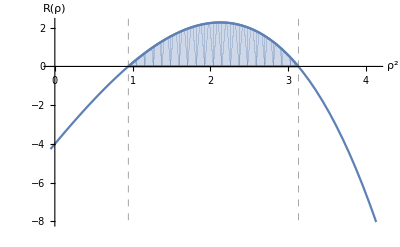

```mathematica
(* Here there is a plot of the polynomial R(ρ^2)=X(x) for the parameters defined on the first cell. This plot is made to show the turning points where the orbits can exist, in dashed gray, while the region is filled. *)
ClearAll[region]
region=RegionPlot[{0<=y<Rpoly[χ,j,ee,ll,k,x]/.orbitparams},{x,rootx0-1,rootlim+1},{y,0,200}];
Show[Plot[Rpoly[χ,j,ee,ll,k,x]/.orbitparams,{x,rootx0-1,rootlim+1},AxesLabel->{"ρ^2","R(ρ)"}],region,GridLines->{{rootx0,rootlim},{}},GridLinesStyle->Directive[Gray, Dashed]]
```

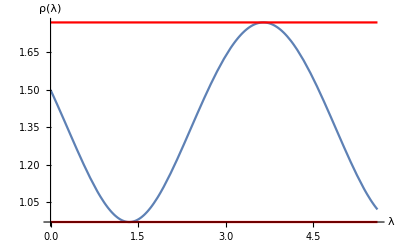

```mathematica
(* In this cell the radial solution is defined. The outuput of this cell shows the radial function in terms of the Mino time. A orbit is bounded between two turning points, which are shown in red lines. *)
ClearAll[v0,vinρ]
v0=1/4(cc3/(ρ0^2-x0)+cc2/3)/.ccparams/.Join[orbitparams,{x0->rootx0}];
vinρ=N[NIntegrate[signρ/(√(4*v^3-gg2*v-gg3))/.weiersparams/.Join[orbitparams,{x0->rootx0}],{v,v0,∞}]+λ0,40];
ClearAll[rho,rholimitsplot,rhoplot]
rho[v_]=√(cc3/(4*WeierstrassP[v,{gg2,gg3}]-cc2/3)+x0)/.Join[weiersparams,ccparams]/.Join[orbitparams,{x0->rootx0}];
rholimitsplot=Plot[{√xlimit1,√xlimit2},{v,vmin,vmax},PlotStyle->Red];
rhoplot=Plot[rho[v-Re[vinρ]],{v,vmin,vmax},AxesLabel->{"λ","ρ(λ)"}];
Show[rhoplot,rholimitsplot]
```

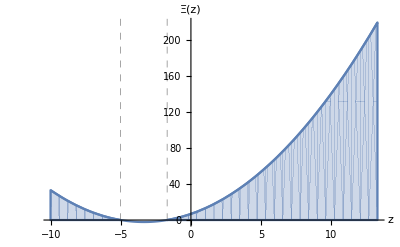

```mathematica
(* Z-motion *)
(* This cell shows the function Ξ(z). The regions of allowed orbit are filled and the turning points are shown in dashed-gray *)
ClearAll[Zpoly,zroots,zliminf,zlimsup,zlimplot,regionz]
Zpoly[z_]:=-k+(ee+4*j*ll*z)^2
zroots=Flatten[Solve[Zpoly[z]==0,z]];
zliminf=z/.zroots[[1]]/.orbitparams;
zlimsup=z/.zroots[[2]]/.orbitparams;
zlimplot=Plot[{zliminf,zlimsup},{v,vmin,vmax}/.orbitparams,PlotStyle->Red];
regionz=RegionPlot[{0<=y<Zpoly[z]}/.orbitparams,{z,zliminf-5,zlimsup+15},{y,0,10000}];
Show[Plot[Zpoly[z]/.orbitparams,{z,zliminf-5,zlimsup+15},AxesLabel->{"z","Ξ(z)"},GridLines->{{zliminf,zlimsup},{}},GridLinesStyle->Directive[Gray, Dashed]],regionz]
```

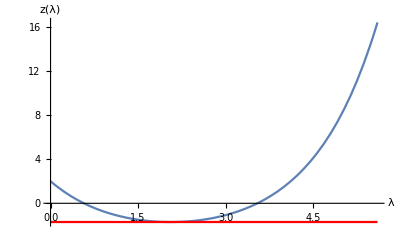

```mathematica
(* Here the solution for Z(λ) is show *)
ClearAll[vinz,z,zplot]
vinz=λ0-signz/(4*j*ll)ArcCosh[(ee+4*j*ll*z0)/(√k)]/.orbitparams;
z[v_]:=1/(4*j*ll)(√k*Cosh[4*j*ll*v]-ee)/.orbitparams
zplot=Plot[z[v-vinz],{v,vmin,vmax}];
Show[zplot,zlimplot,AxesLabel->{"λ","z(λ)"}]
```

```mathematica
(* ϕ-motion *)
(* The two half periods of the radial orbit. ω1 should be real *)
ClearAll[halfper]
halfper=WeierstrassHalfPeriods[{gg2,gg3}/.weiersparams/.Join[orbitparams,{x0->rootx0}]]
```

{2.2964340632776838624841725707453091,3.940837068675355355342457935232562 ⅈ}

```mathematica
(* ϕ-motion is Elliptical integral of third kind. In this cell we are defining the Logaritmical functions of the Weierstrass σ(x) function. In the following cell the solution to the integral of third kind is defined. *)
ClearAll[logtest,logSigma]
logtest[x_,pole_,g2_,g3_]:=Module[{Logreal},
Logreal=Log[WeierstrassSigma[x-pole,{g2,g3}]]-Log[WeierstrassSigma[x+pole,{g2,g3}]]//Chop;
If[Im[Logreal]==0,
		Logreal, 
		NIntegrate[WeierstrassZeta[t-pole,{g2,g3}]-WeierstrassZeta[t+pole,{g2,g3}],{t,0,x}]//Chop
  ]
]
logSigma[x_,pole_,g2_,g3_]:=Module[{η1,ω1,sigmaminus,sigmaplus,cc,kk},
	ω1=WeierstrassHalfPeriods[{g2,g3}][[1]];	
	η1=WeierstrassZeta[ω1,{g2,g3}];
	sigmaminus=WeierstrassSigma[x-pole,{g2,g3}]*Exp[-η1/(2*ω1)*(x-pole)^2];
	sigmaplus=WeierstrassSigma[x+pole,{g2,g3}]*Exp[-η1/(2*ω1)*(x+pole)^2];
	cc=logtest[ω1,pole,g2,g3]-logtest[10^(-10),pole,g2,g3];	
	kk=-ω1/π(Im[2*η1*pole]/ω1+Im[cc]/ω1);
Log[sigmaminus/sigmaplus*Exp[kk*π*ⅈ(x/ω1-1)]]-kk*π*ⅈ(x/ω1-1)-(2*η1*pole*x)/ω1
]
```

```mathematica
ClearAll[dwp,Int1,Int2,Int3]
(* Defining some shortcuts for Weierstrassian functions and derivatives *)
wp[x_,g2_,g3_]=WeierstrassP[x,{g2,g3}];
wζ[x_,g2_,g3_]=WeierstrassZeta[x,{g2,g3}];
dwp[x_,g2_,g3_,p_]:=Module[{y},
D[WeierstrassP[y,{g2,g3}],{y,p}]/.{y->x}
]
(* Integrals of ∫1/(℘(x)-℘(y))^n ⅆx *)
Int1[x_,pole_,g2_,g3_]:=1/dwp[pole,g2,g3,1]*(2*wζ[pole,g2,g3]*x+logSigma[x,pole,g2,g3]);
Int2[x_,pole_,g2_,g3_]:=-dwp[pole,g2,g3,2]/dwp[pole,g2,g3,1]^3*logSigma[x,pole,g2,g3]-(wζ[x+pole,g2,g3]+wζ[x-pole,g2,g3])/dwp[pole,g2,g3,1]^2-((2*wp[pole,g2,g3])/dwp[pole,g2,g3,1]^2+(2*dwp[pole,g2,g3,2]*wζ[pole,g2,g3])/dwp[pole,g2,g3,1]^3)*x
Int3[x_,pole_,g2_,g3_]:=1/(2*dwp[pole,g2,g3,1]^3)(
wp[x+pole,g2,g3]-wp[x-pole,g2,g3]-2*dwp[pole,g2,g3,1]*x-12*wp[pole,g2,g3]*dwp[pole,g2,g3,1]*Int1[x,pole,g2,g3]-3*dwp[pole,g2,g3,1]*dwp[pole,g2,g3,2]*Int2[x,pole,g2,g3]
)
```

```mathematica
(* Obtaining the parameters of the partial fraction decomposition *)
ClearAll[ϕρ]
ϕρ[v_]=Apart[ll*Expand[((1+j^2*ρ^4)^2)/ρ^2/.{ρ->√x}/.{x->1/u+x0}/.{u->1/cc3(4*v-cc2/3)},v],v]
```

(27 cc3^3 j^4 ll)/(-cc2+12 v)^3+(27 cc3^2 j^4 ll x0)/(-cc2+12 v)^2-(3 cc3 ll)/(x0 (3 cc3-cc2 x0+12 v x0))+(ll (1+j^2 x0^2)^2)/x0+(3 (2 cc3 j^2 ll+3 cc3 j^4 ll x0^2))/(-cc2+12 v)

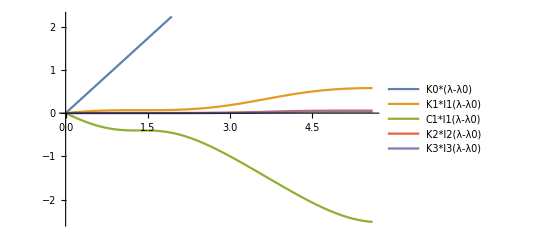

```mathematica
(* Defining the constants, this might be done manually. Remember: the integrals were made from terms of ∫1/(℘(x)-℘(y))^n ⅆx *)
ClearAll[K0,K1,K2,K3,C1]
K0=(ll*(1+j^2*x0^2)^2)/x0/.ccparams/.Join[orbitparams,{x0->rootx0}];
K1=(3*ll*(2 cc3*j^2+3 cc3*j^4*x0^2))/12/.ccparams/.Join[orbitparams,{x0->rootx0}];
C1=-(3*ll* cc3)/(x0 *(12 x0))/.ccparams/.Join[orbitparams,{x0->rootx0}];
K2=(27*cc3^2*j^4*ll* x0)/12^2/.ccparams/.Join[orbitparams,{x0->rootx0}];
K3=(27*cc3^3*j^4*ll)/12^3/.ccparams/.Join[orbitparams,{x0->rootx0}];
(* Defining the two poles of the function *)
ClearAll[pole1,pole2]
pole1=InverseWeierstrassP[cc2/12,{gg2,gg3}]/.Join[ccparams,weiersparams]/.Join[orbitparams,{x0->rootx0}];
pole2=InverseWeierstrassP[(-3*cc3+cc2*x0)/(12*x0),{gg2,gg3}]/.Join[ccparams,weiersparams]/.Join[orbitparams,{x0->rootx0}];
(* A plot of all this components *)
ClearAll[g2,g3]
g2=gg2/.weiersparams/.orbitparams/.{x0->rootx0};
g3=gg3/.weiersparams/.orbitparams/.{x0->rootx0};
Plot[{K0*(v-λ0),
K1*Re[(Int1[v-vinρ,pole1,g2,g3]-Int1[λ0-vinρ,pole1,g2,g3])],
C1*Re[(Int1[v-vinρ,pole2,g2,g3]-Int1[λ0-vinρ,pole2,g2,g3])],
K2*Re[(Int2[v-vinρ,pole1,g2,g3]-Int2[λ0-vinρ,pole1,g2,g3])],
K3*Re[(Int3[v-vinρ,pole1,g2,g3]-Int3[λ0-vinρ,pole1,g2,g3])]},
					{v,vmin,vmax},PlotLegends->{"K0*(λ-λ0)","K1*I1(λ-λ0)","C1*I1(λ-λ0)","K2*I2(λ-λ0)","K3*I3(λ-λ0)"}]
```

```mathematica
ClearAll[Intϕρ]
Intϕρ[v_]:=K0*(v-λ0)+K1*(Int1[v-vinρ,pole1,g2,g3]-Int1[λ0-vinρ,pole1,g2,g3])+C1*(Int1[v-vinρ,pole2,g2,g3]-Int1[λ0-vinρ,pole2,g2,g3])+
K2*(Int2[v-vinρ,pole1,g2,g3]-Int2[λ0-vinρ,pole1,g2,g3])+
K3*(Int3[v-vinρ,pole1,g2,g3]-Int3[λ0-vinρ,pole1,g2,g3])//Re
```

```mathematica
(* ϕz-Component *)
ClearAll[Intϕz]
Intϕz[v_]=1/(16*j*ll^2)(8*j*ll*k(v-λ0)+k*Sinh[8*j*ll*(v-vinz)]-4*ee*√k*Sinh[4*j*ll*(v-vinz)]-(k*Sinh[8*j*ll*(λ0-vinz)]-4*ee*√k*Sinh[4*j*ll*(λ0-vinz)])
			)/.orbitparams;
```

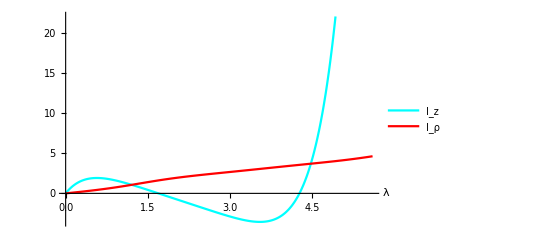

```mathematica
(* Here we can do a comparisson beteween the ϕρ and ϕz components  *)
ClearAll[Plotϕρ,Plotϕz]
Plotϕρ=Plot[Intϕρ[v],{v,vmin,vmax},PlotStyle->Red,PlotLegends->{"I_ρ"}];
Plotϕz=Plot[Intϕz[v],{v,vmin,vmax},PlotStyle->Cyan,PlotLegends->{"I_z"}];
Show[Plotϕz,Plotϕρ,AxesLabel->{"λ",None},PlotRange->All]
```

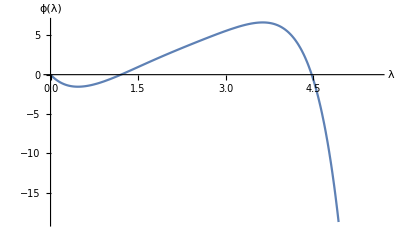

```mathematica
(* Finally defining the ϕ-component *)
ClearAll[phi]
phi[v_]:=Intϕρ[v]-Intϕz[v];
Plot[phi[v],{v,vmin,vmax},AxesLabel->{"λ","ϕ(λ)"}]
```

```mathematica
(* Finally plotting orbits *)
ClearAll[orbit]
orbit=ParametricPlot3D[{rho[v-Re[vinρ]]*Sin[phi[v]],rho[v-Re[vinρ]]*Cos[phi[v]],z[v-vinz]},
							{v,vmin,vmax}, PlotPoints->100,
							AxesLabel->{"x(λ)","y(λ)","z(λ)"},PlotTheme->"Detailed",PlotLegends->False
						]
```

-Graphics3D-

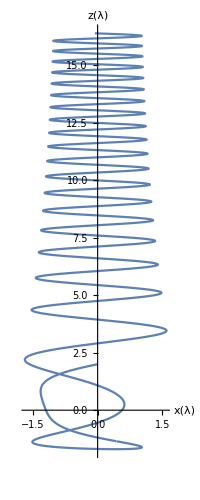
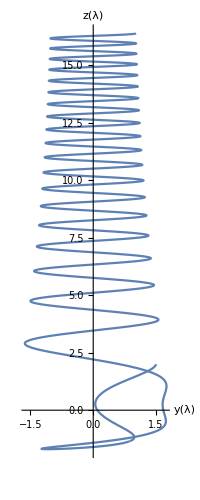
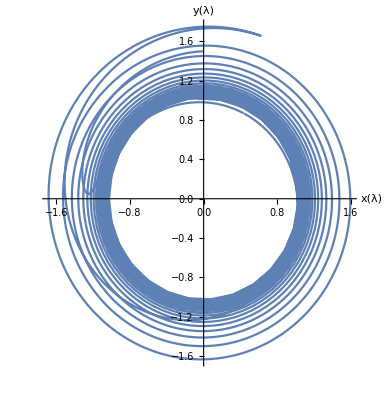

```mathematica
(* Porjections on different planes *)
ClearAll[Xaxes,Yaxes,Zaxes]
Xaxes[v_]=rho[v-Re[vinρ]]*Sin[phi[v]];
Yaxes[v_]=rho[v-Re[vinρ]]*Cos[phi[v]];
Zaxes[v_]=z[v-vinz];
ClearAll[ZXview,ZYview,XYview]
{
ZXview=ParametricPlot[{Xaxes[v],Zaxes[v]},
						{v,vmin,vmax},AxesLabel->{"x(λ)","z(λ)"},
						PlotPoints->100],
ZYview=ParametricPlot[{Yaxes[v],Zaxes[v]},
						{v,vmin,vmax},AxesLabel->{"y(λ)","z(λ)"},
						PlotPoints->100],
XYview=ParametricPlot[{Xaxes[v],Yaxes[v]},
						{v,vmin,vmax},AxesLabel->{"x(λ)","y(λ)"},
						PlotPoints->100]
}
```

```mathematica
(* Exporting *)
Export["ANALYTICAL Orbit 1 massive  j2=1-20 ll=1 k=2.2 ee=3 r0=1.5 z0=2.jpeg",orbit];
Export["ANALYTICAL ZX Orbit 1 massive  j2=1-20 ll=1 k=2.2 ee=3 r0=1.5 z0=2.jpeg",ZXview];
Export["ANALYTICAL ZY Orbit 1 massive  j2=1-20 ll=1 k=2.2 ee=3 r0=1.5 z0=2.jpeg",ZYview];
Export["ANALYTICAL XY Orbit 1 massive  j2=1-20 ll=1 k=2.2 ee=3 r0=1.5 z0=2.jpeg",XYview];
```

```mathematica
(* Proper time integration *)
ClearAll[dτ]
dτ=Expand[(1+j^2*ρ^4)/.{ρ->√x}/.{x->1/u+x0}/.{u->1/cc3(4*v-cc2/3)},v]
```

1+(cc3^2 j^2)/(-cc2/3+4 v)^2+(2 cc3 j^2 x0)/(-cc2/3+4 v)+j^2 x0^2

```mathematica
(* Parameters for proper time integration *)
ClearAll[P0,P1,P2]
P0=1+j^2*x0^2/.Join[orbitparams,{x0->rootx0}];
P1=(2 cc3 j^2 x0)/4/.ccparams/.Join[orbitparams,{x0->rootx0}];
P2=(cc3^2 j^2)/4^2/.ccparams/.Join[orbitparams,{x0->rootx0}];
ClearAll[τ]
τ[v_]=P0*(v-λ0)+P1*(Int1[v-vinρ,pole1,g2,g3]-Int1[λ0-vinρ,pole1,g2,g3])+P2*(Int2[v-vinρ,pole1,g2,g3]-Int2[λ0-vinρ,pole1,g2,g3])//Re;
```

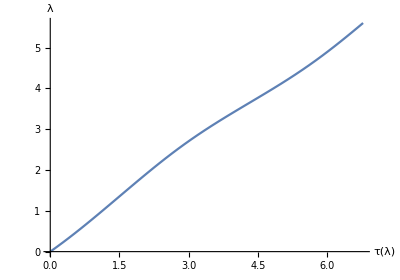
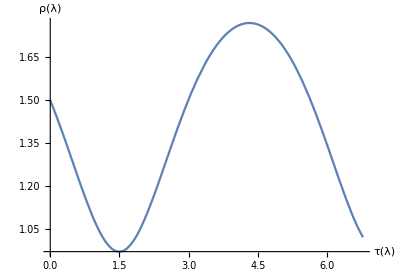
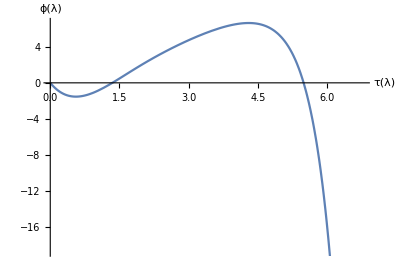
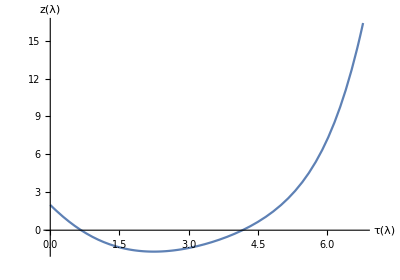

```mathematica
(* Mino-time in terms of proper time and Coordinates in terms of proper time *)
{
ParametricPlot[{τ[v],v},{v,vmin,vmax},AxesLabel->{"τ(λ)","λ"},AspectRatio->.7],
ParametricPlot[{τ[v],rho[v-vinρ]},{v,vmin,vmax},AxesLabel->{"τ(λ)","ρ(λ)"},AspectRatio->.7],
ParametricPlot[{τ[v],phi[v]},{v,vmin,vmax},AxesLabel->{"τ(λ)","ϕ(λ)"},AspectRatio->.7],
ParametricPlot[{τ[v],z[v-vinz]},{v,vmin,vmax},AxesLabel->{"τ(λ)","z(λ)"},AspectRatio->.7]
}
```

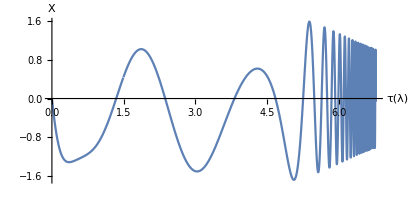
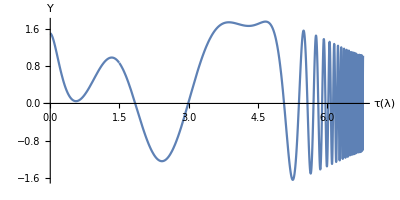

```mathematica
(* X and Y axes in terms of proper time *)
{
ParametricPlot[{τ[v],Xaxes[v]},{v,vmin,vmax},AxesLabel->{"τ(λ)","X"}],
ParametricPlot[{τ[v],Yaxes[v]},{v,vmin,vmax},AxesLabel->{"τ(λ)","Y"}]
}
```

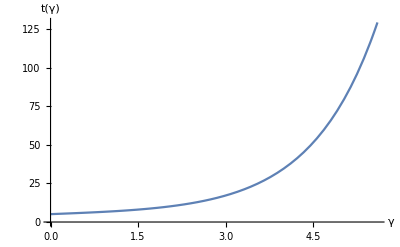
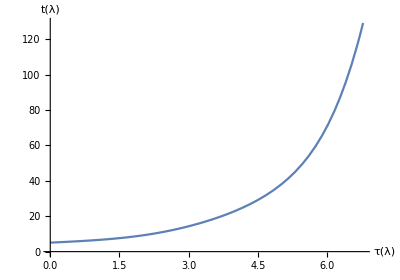

```mathematica
(* Solution of the time coordinate in terms of Mino time and proper time *)
ClearAll[t,t0,tin]
t0=0;
tin=t0-(√k)/(4*j*ll)Sinh[4*j*ll*(λ0-vinz)]/.orbitparams;
t[v_]:=(√k)/(4*j*ll)Sinh[4*j*ll*v]/.orbitparams
{
Plot[t[v]+tin,{v,vmin,vmax},AxesLabel->{"γ","t(γ)"}],
ParametricPlot[{τ[v],t[v]+tin},{v,vmin,vmax},AxesLabel->{"τ(λ)","t(λ)"},AspectRatio->0.7]
}
```